```mathematica
Clear["Global`*"]
```

```mathematica
Get["IGraphM`"]
```

IGraph/M 0.3.110 (April 22, 2019)

Evaluate IGDocumentation[] to get started.

1 - 7 Bipartite or not?
If your answer is yes, find S and T.

1.  Problem represented by a diagram.

```mathematica
g1=Graph[{1<->2,1<->3,3<->2},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{0,-1}},ImageSize->100]
```

-Graphics-

No not bipartite.

3.  Problem represented by a diagram.

```mathematica
g3=Graph[{1<->2,1<->3,3<->2,1<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{0,-1},{1,-1}},ImageSize->100]
```

-Graphics-

No not bipartite.

5.  Problem represented by a diagram.

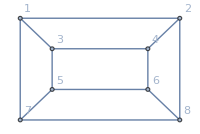

```mathematica
g5=Graph[{1<->2,2<->8,8<->7,1<->7,1<->3,3<->4,4<->6,6<->5,5<->3,2<->4,7<->5,6<->8},VertexLabels->"Name",VertexCoordinates->{{0,0},{1.5,0},{1.5,-1},{0,-1},{0.3,-0.3},{1.2,-0.3},{1.2,-0.7},{0.3,-0.7}},ImageSize->200]
```

Yes, bipartite.

7.

```mathematica
g7=Graph[{1<->2,1<->3,3<->4,4<->5,5<->6,6<->1,2<->5,1<->4,6<->3},VertexLabels->"Name",VertexCoordinates->{{0,0},{0.5,0},{1,0},{1,-1},{0.5,-1},{0,-1}},ImageSize->100]
```

-Graphics-

Yes, bipartite.

10 - 12 Matching augmenting paths
Find an augmenting path:

11.  Problem represented by a diagram.

On p. 1003 of the text is an algorithm for finding augmenting paths and maximizing cardinality matching.  Although the algorithm works well in example 1 on p. 1004, there are a few hiccups in this problem, mostly revolving around the text answer. After a fairly lengthy process of trying various augmenting strategies, I then substitute a couple of IG commands which shortcut augmenting paths to determine the maximum matching cardinality.

Part A: In which I try to come up with the text answer.

```mathematica
g11a=HighlightGraph[Graph[{1<->2,1<->4,3<->2,3<->6,4<->5,5<->7,1<->6,3<->7,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-0.6},{0,-0.7},{1,-1.3},{0,-1.3},{1,-1.9}},ImageSize->130],{2<->3,5<->7},GraphHighlightStyle->"Thick",ImagePadding->15];
```

```mathematica
t1=Graphics[{{White,Rectangle[{0,0},{14,2}]},{Text[Style["In the initial plot, the M_1 matching is shown
 as two highlighted edges.",Medium],{2,1.5}]}},ImageSize->600];
```

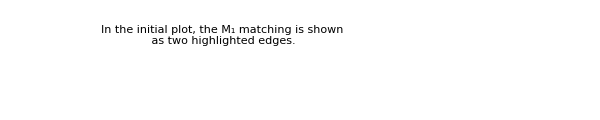
-Graphics--Graphics-

```mathematica
Row[{g11a,t1}]
```

```mathematica
g11b=HighlightGraph[Graph[{1<->2,1<->4,3<->2,3<->6,4<->5,5<->7,1<->6,3<->7,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-0.6},{0,-0.7},{1,-1.3},{0,-1.3},{1,-1.9}},ImageSize->130,Epilog->{Text[Style["Ø",Medium],{-0.1,0}]}],{2<->3,5<->7},GraphHighlightStyle->"Thick",ImagePadding->15];
```

```mathematica
t2=Graphics[{{White,Rectangle[{0,0},{14,2}]},{Text[Style["Step 1: In the left bipartite partition (1,3,5)
the exposed vertex is marked with the symbol Ø.",Medium],{2,1.5}]}},ImageSize->600];
```

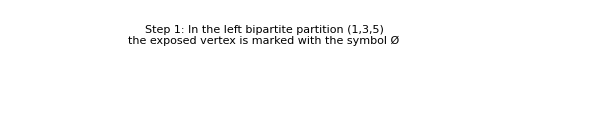
-Graphics--Graphics-

```mathematica
Row[{g11b,t2}]
```

```mathematica
g11c=HighlightGraph[Graph[{1<->2,1<->4,3<->2,3<->6,4<->5,5<->7,1<->6,3<->7,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-0.6},{0,-0.7},{1,-1.3},{0,-1.3},{1,-1.9}},ImageSize->130,Epilog->{{Blue,Text[Style["Ø",Medium],{-0.1,0}]},{Blue,Text[Style["5",Bold,Medium],{1.13,-0.6}]},{Blue,Text[Style["1",Bold,Medium],{1.13,-1.31}]},{Blue,Text[Style["1",Bold,Medium],{1.13,0}]},{Blue,Text[Style["3",Bold,Medium],{1.13,-1.9}]}}],{2<->3,5<->7},GraphHighlightStyle->"Thick",ImagePadding->15];
```

```mathematica
t3=Graphics[{{White,Rectangle[{0,0},{14,2}]},{Text[Style["Step 2: In the right bipartite partition (2,4,6,7)
edge terminal vertices are labeled with first
 available (connecting) left vertex which
 does not belong to M_1. This seems to be
 a defect in the problem, because vertex 4 needs
to have label 5. So edges 1<->4 and 3<->4
must not exist. (Vertex review in S starting
 at the bottom does not work either.)
Thus the text answer or text diagram
 is suspect.",Medium],{4,1.5}]}},ImageSize->600];
```

```mathematica
Row[{g11c,t3}]
```

-Graphics--Graphics-

```mathematica
g11d=HighlightGraph[Graph[{1<->2,1<->4,3<->2,3<->6,4<->5,5<->7,1<->6,3<->7,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-0.6},{0,-0.7},{1,-1.3},{0,-1.3},{1,-1.9}},ImageSize->130,Epilog->{{Blue,Text[Style["Ø",Medium],{-0.1,0}]},{Blue,Text[Style["5",Bold,Medium],{1.13,-0.6}]},{Blue,Text[Style["1",Bold,Medium],{1.13,-1.31}]},{Blue,Text[Style["1",Bold,Medium],{1.13,0}]},{Blue,Text[Style["3",Bold,Medium],{1.13,-1.9}]},{Blue,Text[Style["2",Bold,Medium],{-0.1,-0.7}]},{Blue,Text[Style["7",Bold,Medium],{-0.1,-1.3}]},{Blue,Thickness[0.017],Line[{{0,-0.7},{1,-0.6}}]},{Blue,Thickness[0.017],Line[{{0,0},{1,-0.6}}]}}],{2<->3,5<->7},GraphHighlightStyle->"Thick",ImagePadding->15];
```

```mathematica
t4=Graphics[{{White,Rectangle[{0,0},{14,2}]},{Text[Style["Step 3: The left unlabeled vertices are part of M_1.
 They are labeled to reflect the corresponding
 M_1 right vertices. The blue edges are
being ignored, as explained in the
last step, so that the label 5
can be put where it needs to be.",Medium],{4,1.5}]}},ImageSize->600];
```

```mathematica
Row[{g11d,t4}]
```

-Graphics--Graphics-

```mathematica
g11e=HighlightGraph[Graph[{1<->2,1<->4,3<->2,3<->6,4<->5,5<->7,1<->6,3<->7,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-0.6},{0,-0.7},{1,-1.3},{0,-1.3},{1,-1.9}},ImageSize->130,Epilog->{{Blue,Text[Style["Ø",Medium],{-0.1,0}]},{Blue,Text[Style["5",Bold,Medium],{1.13,-0.6}]},{Blue,Text[Style["1",Bold,Medium],{1.13,-1.31}]},{Blue,Text[Style["1",Bold,Medium],{1.13,0}]},{Blue,Text[Style["3",Bold,Medium],{1.13,-1.9}]},{Blue,Text[Style["2",Bold,Medium],{-0.1,-0.7}]},{Blue,Text[Style["7",Bold,Medium],{-0.1,-1.3}]},{Green,Dashed,Thickness[0.017],Line[{{0,0},{1,0},{0,-0.7},{1,-1.9},{0,-1.3},{1,-0.6}}]},{Blue,Thickness[0.017],Line[{{0,0},{1,-0.6}}]}}],{2<->3,5<->7},GraphHighlightStyle->"Thick",ImagePadding->15];
```

```mathematica
t5=Graphics[{{White,Rectangle[{0,0},{14,2}]},{Text[Style["Step 4: This is the backtracking step.
The text answer is 1-2-3-7-5-4.
Following the dashed green line, produces
an augmenting path.",Medium],{4,1.5}]}},ImageSize->600];
```

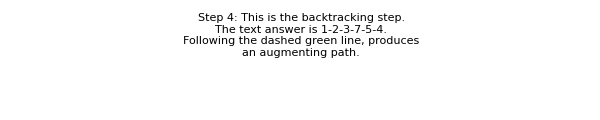
-Graphics--Graphics-

```mathematica
Row[{g11e,t5}]
```

```mathematica
g11f=HighlightGraph[Graph[{1<->2,1<->4,3<->2,3<->6,4<->5,5<->7,1<->6,3<->7,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-0.6},{0,-0.7},{1,-1.3},{0,-1.3},{1,-1.9}},ImageSize->130],{1<->2,3<->7,5<->4},GraphHighlightStyle->"Thick",ImagePadding->15];
```

```mathematica
t6=Graphics[{{White,Rectangle[{0,0},{14,2}]},{Text[Style["Step 5: This is the reconfiguration step.
In the previous figure, the red M_1 edges show
 through the green. These are to be dropped,
 and the other green edges are the new M_2.

Step 6. Ready for another iteration. However,
there are no more exposed vertices in S.
Therefore I am finished, and the final,
max cardinality is three.",Medium],{4,1.5}]}},ImageSize->600];
```

```mathematica
Row[{g11f,t6}]
```

-Graphics--Graphics-

Part B: In which I barge ahead without trying to reproduce the text answer.

```mathematica
g11g=HighlightGraph[Graph[{1<->2,1<->4,3<->2,3<->6,4<->5,5<->7,1<->6,3<->7,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-0.6},{0,-0.7},{1,-1.3},{0,-1.3},{1,-1.9}},ImageSize->130,Epilog->{Text[Style["Ø",Medium],{-0.1,0}]}],{2<->3,5<->7},GraphHighlightStyle->"Thick",ImagePadding->15];
```

```mathematica
t7=Graphics[{{White,Rectangle[{0,0},{14,2}]},{Text[Style["Step 1: In the left bipartite partition (1,3,5)
the exposed vertex is marked with the symbol Ø.
This step unchanged from Part A.",Medium],{2,1.5}]}},ImageSize->600];
```

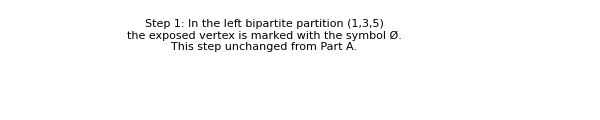
-Graphics--Graphics-

```mathematica
Row[{g11g,t7}]
```

```mathematica
g11h=HighlightGraph[Graph[{1<->2,1<->4,3<->2,3<->6,4<->5,5<->7,1<->6,3<->7,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-0.6},{0,-0.7},{1,-1.3},{0,-1.3},{1,-1.9}},ImageSize->130,Epilog->{{Blue,Text[Style["Ø",Medium],{-0.1,0}]},{Blue,Text[Style["1",Bold,Medium],{1.13,-0.6}]},{Blue,Text[Style["1",Bold,Medium],{1.13,-1.31}]},{Blue,Text[Style["1",Bold,Medium],{1.13,0}]},{Blue,Text[Style["3",Bold,Medium],{1.13,-1.9}]}}],{2<->3,5<->7},GraphHighlightStyle->"Thick",ImagePadding->15];
```

```mathematica
t8=Graphics[{{White,Rectangle[{0,0},{14,2}]},{Text[Style["Step 2: In the right bipartite partition (2,4,6,7)
edge terminal vertices are labeled with first
 available (connecting) left vertex, without
retracing M_1edges.",Medium],{4,1.5}]}},ImageSize->600];
```

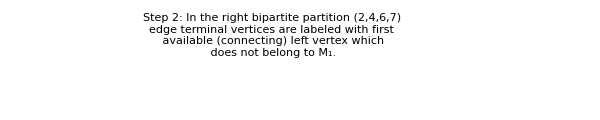
-Graphics--Graphics-

```mathematica
Row[{g11h,t8}]
```

```mathematica
g11i=HighlightGraph[Graph[{1<->2,1<->4,3<->2,3<->6,4<->5,5<->7,1<->6,3<->7,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-0.6},{0,-0.7},{1,-1.3},{0,-1.3},{1,-1.9}},ImageSize->130,Epilog->{{Blue,Text[Style["Ø",Medium],{-0.1,0}]},{Blue,Text[Style["1",Bold,Medium],{1.13,-0.6}]},{Blue,Text[Style["1",Bold,Medium],{1.13,-1.31}]},{Blue,Text[Style["1",Bold,Medium],{1.13,0}]},{Blue,Text[Style["3",Bold,Medium],{1.13,-1.9}]},{Blue,Text[Style["2",Bold,Medium],{-0.1,-0.7}]},{Blue,Text[Style["7",Bold,Medium],{-0.1,-1.3}]}}],{2<->3,5<->7},GraphHighlightStyle->"Thick",ImagePadding->15];
```

```mathematica
t9=Graphics[{{White,Rectangle[{0,0},{14,2}]},{Text[Style["Step 3: The left unlabeled vertices are part of M_1.
 They are labeled to reflect the corresponding
 M_1 right vertices.",Medium],{4,1.5}]}},ImageSize->600];
```

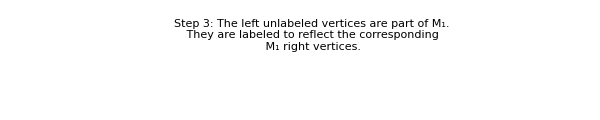
-Graphics--Graphics-

```mathematica
Row[{g11i, t9}]
```

```mathematica
g11j=HighlightGraph[Graph[{1<->2,1<->4,3<->2,3<->6,4<->5,5<->7,1<->6,3<->7,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-0.6},{0,-0.7},{1,-1.3},{0,-1.3},{1,-1.9}},ImageSize->130,Epilog->{{Blue,Text[Style["Ø",Medium],{-0.1,0}]},{Blue,Text[Style["1",Bold,Medium],{1.13,-0.6}]},{Blue,Text[Style["1",Bold,Medium],{1.13,-1.31}]},{Blue,Text[Style["1",Bold,Medium],{1.13,0}]},{Blue,Text[Style["3",Bold,Medium],{1.13,-1.9}]},{Blue,Text[Style["2",Bold,Medium],{-0.1,-0.7}]},{Blue,Text[Style["7",Bold,Medium],{-0.1,-1.3}]},{Green,Dashed,Thickness[0.017],Line[{{0,0},{1,0},{0,-0.7},{1,-1.9},{0,-1.3}}]}}],{2<->3,5<->7},GraphHighlightStyle->"Thick",ImagePadding->15];
```

```mathematica
t10=Graphics[{{White,Rectangle[{0,0},{14,2}]},{Text[Style["Step 4: This is the backtracking step.
The text answer is 1-2-3-7-5-4.
Following the dashed green line, produces
a pseudo-augmenting path, stopping
at vertex 5. The reason it is 'pseudo' 
is explained in the next step.",Medium],{4,1.5}]}},ImageSize->600];
```

```mathematica
Row[{g11j,t10}]
```

-Graphics--Graphics-

```mathematica
g11k=HighlightGraph[Graph[{1<->2,1<->4,3<->2,3<->6,4<->5,5<->7,1<->6,3<->7,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-0.6},{0,-0.7},{1,-1.3},{0,-1.3},{1,-1.9}},ImageSize->130],{1<->2,3<->7},GraphHighlightStyle->"Thick",ImagePadding->15];
```

```mathematica
t11=Graphics[{{White,Rectangle[{0,0},{14,2}]},{Text[Style["Step 5: This is the reconfiguration step.
In the previous figure, the red M_1 edges show
 through the green. These are to be dropped,
 and the other green edges are the new M_2. Unfortunately,
M_2has only two edges, short of the max.
",Medium],{4,1.5}]}},ImageSize->600];
```

```mathematica
Row[{g11k,t11}]
```

-Graphics--Graphics-

```mathematica
g11l=HighlightGraph[Graph[{1<->2,1<->4,3<->2,3<->6,4<->5,5<->7,1<->6,3<->7,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-0.6},{0,-0.7},{1,-1.3},{0,-1.3},{1,-1.9}},ImageSize->130,Epilog->{{Blue,Text[Style["2",Medium],{-0.1,0}]},{Blue,Text[Style["5",Bold,Medium],{1.13,-0.6}]},{Blue,Text[Style["3",Bold,Medium],{1.13,-1.31}]},{Blue,Text[Style["3",Bold,Medium],{1.13,0}]},{Blue,Text[Style["5",Bold,Medium],{1.13,-1.9}]},{Blue,Text[Style["7",Bold,Medium],{-0.1,-0.7}]},{Blue,Text[Style["Ø",Bold,Medium],{-0.1,-1.3}]}(*,{Green,Dashed,Thickness[0.017],Line[{{0,0},{1,0},{0,-0.7},{1,-1.9},{0,-1.3}}]}*)}],{1<->2,3<->7},GraphHighlightStyle->"Thick",ImagePadding->15];
```

```mathematica
t12=Graphics[{{White,Rectangle[{0,0},{14,2}]},{Text[Style["Step 6: Ready for another iteration, and
there is still an exposed edge.
Compressing a few steps, it is apparent
that 5<->7 or 5<->4 will be added to the matching,
in a single-edge augmenting path,
and that the max cardinality of 3 will be reached.",Medium],{4,1.5}]}},ImageSize->600];
```

```mathematica
Row[{g11l,t12}]
```

-Graphics--Graphics-

Part C: Alternative and miscellaneous.

For curiosity, I show what a bfs table for the graph would look like.

```mathematica
Grid[Table[BreadthFirstScan[g11,n],{n,1,7}],Frame->All]
```

1 | 1 | 1 | 2 | 1 | 4 | 3
2 | 2 | 1 | 2 | 1 | 4 | 3
2 | 3 | 3 | 3 | 3 | 7 | 3
4 | 1 | 4 | 4 | 1 | 4 | 5
4 | 1 | 5 | 4 | 1 | 5 | 5
6 | 3 | 3 | 6 | 6 | 7 | 3
4 | 3 | 5 | 7 | 3 | 7 | 7

The purpose of finding augmenting paths, I believe, is to maximize the cardinality matching. The following two cells determine the maximum cardinality for this graph, and display one version of M.

```mathematica
IGMatchingNumber[g11]
```

3

```mathematica
IGMaximumMatching[g11]
```

{5<->7,3<->6,1<->4}

Below is the highlighted graph showing the maximum cardinality matching chosen by IG.

```mathematica
HighlightGraph[g11,IGMaximumMatching[g11],GraphHighlightStyle->"Thick",ImagePadding->15]
```

-Graphics-

13 - 15 Maximum cardinality matching
Using augmenting paths, find a maximum cardinality matching:

13.  In problem 11.

This has been done above.

15. In problem 12.

The below graph is the one that concerns problem 12.

```mathematica
g15=Graph[{1<->2,4<->3,3<->6,2<->3,5<->6,6<->7,5<->8,7<->8,2<->5},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-0.6},{0,-0.7},{1,-1.3},{0,-1.3},{0,-1.9},{1,-1.9}},ImageSize->120]
```

-Graphics-

The below three commands find the maximum matching cardinality, a representative matching, and the graph with representative matching highlighted.

```mathematica
IGMatchingNumber[g15]
IGMaximumMatching[g15]
HighlightGraph[g15,IGMaximumMatching[g15],GraphHighlightStyle->"Thick",ImagePadding->15]
```

4

{7<->8,5<->6,4<->3,1<->2}

-Graphics-

19 - 25 Vertex coloring

19.  Vertex coloring and exam scheduling. What is the smallest number of exam periods for six subjects a, b, c, d, e, f if some of the students simultaneously take a, b, f, some c, d, e, some a, c, e, and some c, e? Solve this as follows. Sketch a graph with six vertices a, . . . , f and join vertices if they represent subjects simultaneously taken by some students. Color the vertices so that adjacent vertices receive different colors. (Use numbers 1, 2, . . . instead of actual colors if you want.) What is the minimum number of colors you need? For any graph G, this minimum number is called the (vertex) chromatic number Χ_ν(G). Why is this the answer to the problem? Write down a possible schedule.

I stared at this awhile, and experimented with several possible approaches, but did not find one satisfactory. Just by “inspection” though, it is not that difficult. First, since some students are taking blocks of 3 of 6 courses, it is obvious that at least three separate test periods will be required. On the other hand, no student would encounter an incompatibility if only three periods were made available for testing. In this group of courses and students no insurmountable conflict exists. So one possible schedule is the following:

```mathematica
Grid[{{"9 am","c","f"},{"10 am" ,"e","b"},{"11 am","a","d"}},Frame->All]
```

9 am | c | f
10 am | e | b
11 am | a | d

But suppose that some student was taking the block c, e, f ? Then there would be a conflict, even though no student was enrolled in more than three courses. Something like the following would then be necessary.

```mathematica
Grid[{{"8 am","c"},{"9 am" ,"e","b"},{"10 am","a","d"},{"11 am","f"} },Frame->All]
```

8 am | c | 
9 am | e | b
10 am | a | d
11 am | f |

And with the addition of just two other students, the six courses could require six exam periods. I would be happy to learn how a function or two could calculate this systematically, because on larger problems it would be difficult or impossible to separate the exclusions in my head.

21.  How many colors do you need for vertex coloring any tree?

If the tree is 2-dimensional, I need four colors for this.

22. Harbor management. How many piers does a harbor master need for accommodating six cruise ships S_1, . . .,S_6 with expected dates of arrival A and departure D in July, (A,D) = (10, 13), (13, 15), (14, 17), (12, 15), (16, 18), (14, 17), respectively, if each pier can accommodate only one ship, arrival being at 6 am and departures at 11 pm? Hint. Join S_i and S_j by an edge if their intervals overlap. Then color vertices.

23. What would be the answer to problem 22 if only the five ships S_1, . . . ,S_5 had to be accommodated?

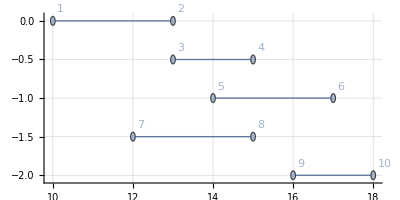

```mathematica
g23=Graph[{1<->2,3<->4,5<->6,7<->8,9<->10},VertexLabels->"Name",VertexCoordinates->{{10,0},{13,0},{13,-0.5},{15,-0.5},{14,-1},{17,-1},{12,-1.5},{15,-1.5},{16,-2},{18,-2}},ImageSize->400,Axes->True,GridLines->Automatic,Epilog->{{Text[Style["P1",Medium],{18.5,0}]},{Text[Style["P2",Medium],{18.5,-0.5}]},{Text[Style["P1",Medium],{18.5,-1}]},{Text[Style["P3",Medium],{18.5,-1.5}]},{Text[Style["P3",Medium],{18.5,-2}]}},ImagePadding->20]
```

Only three piers will be required, as confirmed by the text answer.

24. Four- (vertex) color theorem. The famous four-color theorem states that one can color the vertices of any planar graph (so that adjacent vertices get different colors) with at most four colors. It had been conjectured for a long time and was eventually proved in 1976 by Appel and Haken [Illinois J. Math 21 (1977), 429-567]. Can you color the complete graph K_5 with four colors? Does the result contradict the four-color theorem? (For more details, see reference [F1] in appendix 1.)

25.  Find a graph, as simple as possible, that cannot be vertex colored with three colors. Why is this of interest in connection with problem 24?

How about this one?

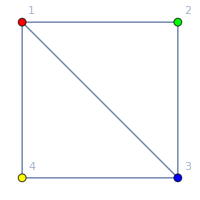

```mathematica
g23=Graph[{1<->2,2<->3,3<->4,4<->1,1<->3},VertexLabels->"Name",VertexCoordinates->{{0,0},{1,0},{1,-1},{0,-1}},ImageSize->200,ImagePadding->20,VertexStyle->{1->Red,2->Green,3->Blue,4->Yellow},VertexSize->0.05]
```